## Assymmetric Molecule: Dispersion

```mathematica
ClearAll["Global`*"]
Ω[μ_]:=({{ω1[μ], -J12, 0}, {-J12, ω2[μ], -J23}, {0, -J23, ω3[μ]}});
```

```mathematica
ω1[μ_]:=ω0 +d1×μ + d2/2 μ^2;
ω2[μ_]:=ω0 +D1×(2μ) + D2/2(2μ)^2;
ω3[μ_]:=ω0+d1×μ + d2/2 μ^2 ;
```

```mathematica
d1 = 400;
D1 = 400/2.03;
d2 =-0.015;
D2 = -0.015;
ω0 = 0;
J12=2;
J23=2;
```

```mathematica
{vals,vecs}=Eigensystem[Ω[μ]];
pairs=Transpose[{vals,vecs}];
sortedEig[μ_]:=SortBy[pairs,First];
```

```mathematica
(*sortedEig[μ_]:=sortedEig[μ]=Module[{vals,vecs,pairs,fixSign},(*flip sign if the first component is negative*)
fixSign[v_]:=v/Sign[v[[1]]];
{vals,vecs}=Eigensystem[Ω[μ]];
vecs=fixSign/@vecs;
pairs=Transpose[{vals,vecs}];
SortBy[pairs,First]];*)
```

```mathematica
ωS[μ_]:=sortedEig[μ][[1,1]]
bS[μ_]:=Normalize[sortedEig[μ][[1,2]]];

ωC[μ_]:=sortedEig[μ][[2,1]];
bC[μ_]:=Normalize[sortedEig[μ][[2,2]]];

ωAS[μ_]:=sortedEig[μ][[3,1]];
bAS[μ_]:=Normalize[sortedEig[μ][[3,2]]];

bAS[0];
```

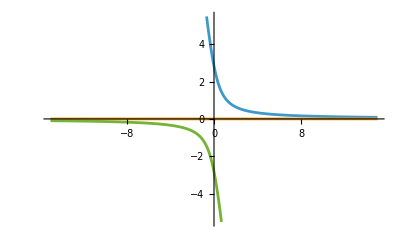

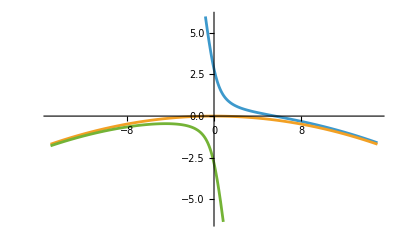

```mathematica
Plot[{ωAS[μ]-ωC[μ],ωC[μ]-ωC[μ],ωS[μ]-ωC[μ]}, {μ,-15,15}]
Plot[{ωAS[μ]-d1×μ,ωC[μ]-d1×μ,ωS[μ]-d1×μ}, {μ,-15,15}]
```

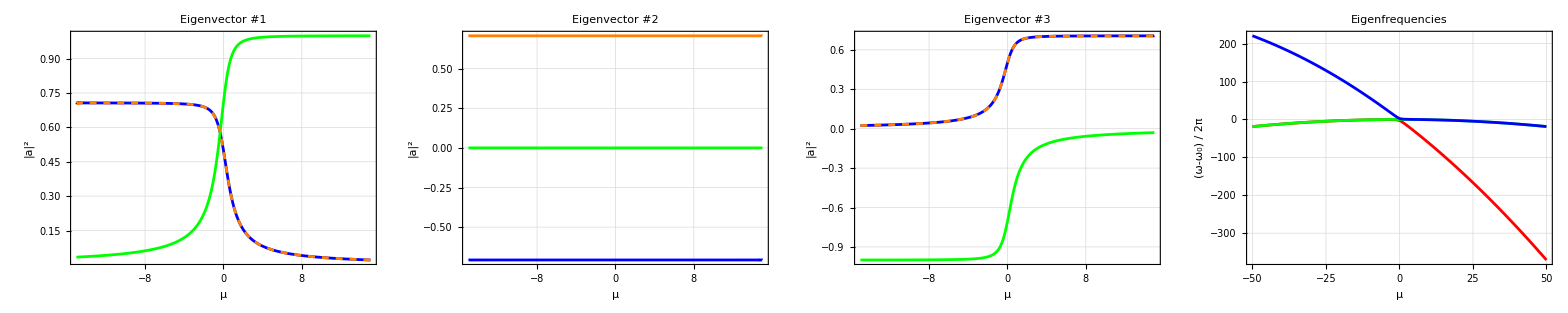

```mathematica
plt1=Plot[{bS[μ][[1]],bS[μ][[2]],bS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #1",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt2=Plot[{bC[μ][[1]],bC[μ][[2]],bC[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #2",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Blue,Green,Orange}];
plt3=Plot[{bAS[μ][[1]],bAS[μ][[2]],bAS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #3",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt4=Plot[{ωS[μ]-d1×μ,ωC[μ]-d1×μ,ωAS[μ]-d1×μ},{μ,-50,50},FrameLabel->{"μ","(ω-ω_0) / 2π"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Red,Green,Blue}];
Grid[{{plt1,plt2,plt3,plt4}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]
```

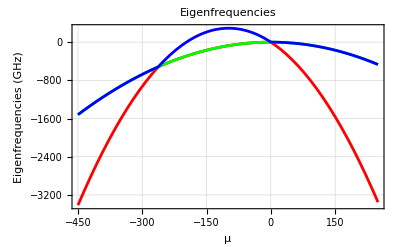

```mathematica
Plot[{ωS[μ]-d1×μ,ωC[μ]-d1×μ,ωAS[μ]-d1×μ},{μ,-450,250},FrameLabel->{"μ","Eigenfrequencies (GHz)"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Red,Green,Blue}]
```

## Overlapping

#### Overlap with central supermode

```mathematica
a1={1,0,0};ΓS[μ_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
ΓC[μ_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bC[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
ΓAS[μ_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bAS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
Γa1[μ_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[a1[[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
```

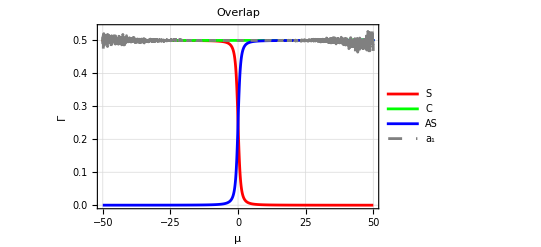

```mathematica
Plot[{ΓS[μ],ΓC[μ],ΓAS[μ], Γa1[μ]},{μ,-50,50},FrameLabel->{"μ","Γ"},PlotLabel->"Overlap",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue,{Gray,Dashed}},PlotLegends->{"S", "C", "AS", "a_1"}]
```